```mathematica
R0=2.5kOhm
```

2.5 kOhm

## u = U/U0 , r=R/R0 , relative unitless values + we only change one resistor -Graphics-

```mathematica
I1=U/(R+R);
I2 = U/(R+R+d R);
U1 = I1*R;
U2 =I2*(R+d R);
du = (U2-U1)/U
Simplify[du]
```

(-U/2+((R+d R) U)/(2 R+d R))/U

d/(4+2 d)

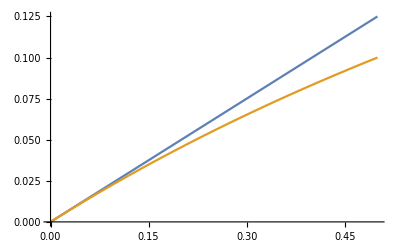

```mathematica
Plot[{d/4,du},{d,0,0.5}]
```

So relatively small (or not?) non - linear effect present there

#### Ok, so what do we get if we short-circuit it

```mathematica
ClearAll["Global'*"]
```

```mathematica
system = {I1u==I1d-Ix,I2u==I2d+Ix,I1d*R == I2d (R+d R),I1u==I2u,I1u R + I1d R==U}
```

{I1u==I1d-Ix,I2u==I2d+Ix,I1d R==I2d (R+d R),I1u==I2u,I1d R+I1u R==U}

```mathematica
Solve[system,{I1u,Ix,I2u,I1d,I2d}]
```

{{I1u→((2+d) U)/((4+3 d) R),Ix→(d U)/((4+3 d) R),I2u→((2+d) U)/((4+3 d) R),I1d→(2 (1+d) U)/((4+3 d) R),I2d→(2 U)/((4+3 d) R)}}

#### Equivalent Resistance of this Voltage Source should be U (open) =du*U / Ix (short circuit)

```mathematica
((U*du)/Ix)/.%[[1]]
```

((4+3 d) R (-U/2+((R+d R) U)/(2 R+d R)))/(d U)

```mathematica
Simplify[%]/.d->0
```

R

#### So resistance = R, a resistance of one of the shoulders. (? is that the word?)